### Line up LHS and RHS columns Increase size of vertices on RH column Possibly put low opacity horizontal guide lines

For Developer

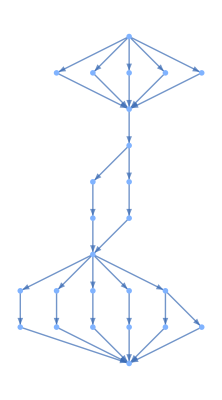

```mathematica
GraphicsRow[{GraphicsColumn[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Gray},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],Thick,Red]]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]],PatternsLayeredGraph[$LifeData["Worker bee"]]},Spacings->20]
```

Increased vertex size, made arrows visible, lined up steps, divider lines are going to have to be  hacky because graphics row doesn’t let me adjust the size of the graph so waiting on those

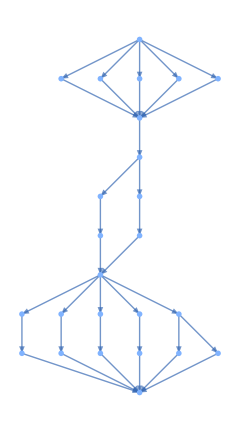
-Graphics--Graphics-

```mathematica
Row[{GraphicsColumn[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Gray},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],Thick,Red]]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9], ImageSize->60],(*Rasterize[*)GraphPlot[PatternsLayeredGraph[$LifeData["Worker bee"], Automatic, "VertexSizeFunction"-> (4Dimensions[#]&), ImageSize-> 240], PlotRangePadding->{Automatic, {0,1}}](*]*)
}, Spacer[10]]
```

### Clean up Include the years here

For Developer

```mathematica
allimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
GraphicsRow[Column[{BoundingBoxLayeredGraph[#],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->12 Sqrt[Last[Dimensions[#MatrixData]]]]},Center]&/@SortBy[allimps[[15]],#Year&],Frame->All,FrameStyle->Opacity[.2],Spacings->30]
```

Increased column spacing, added years, increased size of history plot

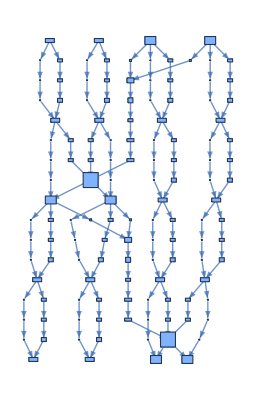
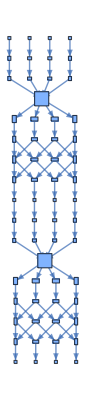
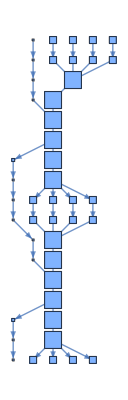
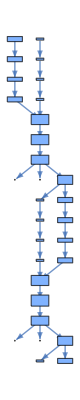
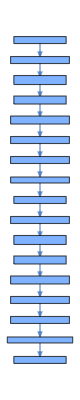
1983 | 1994 | 1994 | 2016 | 2020
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

```mathematica
Grid[{
Style[Text[#Year], 11]&/@SortBy[allimps[[15]],#Year&],
Column[{
BoundingBoxLayeredGraph[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&]},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All, {True, False, True}}, Alignment->Center, Spacings->{1, 1.5}]
```

### Color the dots by red=first of each period, blue=smallest, gray=in between

For Developer (done below?)

Yep SW crushed this out, but we’re going to use the line plot

### Get all vectors for spaceships

For Developer

(This function is in Code-08)

#### v2 getvector

```mathematica
ClearAll@getvector
getvector[data_, t_:Automatic]:= Reverse[First[Total[#]/Length[#]]]*-1&[Differences[(CoordinateBoundingBox[Position[#, 1]]&/@ (CellularAutomaton["GameOfLife",{data["MatrixData"],0},If[t === Automatic, Min[5data["Period"], 5000], t]]))]]
allsimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Spaceship"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

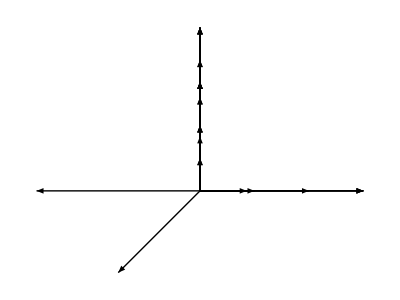

```mathematica
Graphics[Catenate[Map[Arrow[{{0, 0}, #}]&[getvector[#]]&,allsimps, {2}]]]
```